# Brainstorming for Systematic Randomness Testing

```mathematica
rule30seq=CellularAutomaton[30, {{1}, 0}, {10000,0}]ᵀ⟦1⟧;
```

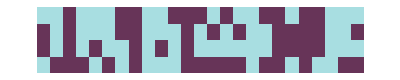

```mathematica
ArrayPlot[Partition[Take[rule30seq,100],25],]
```

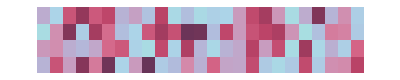

```mathematica
ArrayPlot[Partition[RandomReal[{0,1},100],25],]
```

```mathematica
Autocorrelation
Recurrence quantification analysis
Recurrence plots
AutocorrelationTest
```

http://www-users.math.umn.edu/~garrett/students/reu/pRNGs.pdf

★

https://en.wikipedia.org/wiki/Kolmogorov% E2 %80 %93 Smirnov_test #Kolmogorov % E2 %80 %93 Smirnov_statistic

https://en.wikipedia.org/wiki/Wald% E2 %80 %93 Wolfowitz_runs _test

https://en.wikipedia.org/wiki/Diehard_tests

https://doc.lagout.org/science/0_Computer %20 Science/2_Algorithms/The%20 Art %20 of %20 Computer %20 Programming %20 %28 vol.%202_ %20 Seminumerical %20 Algorithms %29 %20 %283 rd %20 ed.%29%20 %5 BKnuth %201997-11-14%5 D.pdf

An ultimate report

Bin size vs. p-value

## ✓✓ Chi Square Test ★

### Chi Square test for independence — Sequences of 0s and 1s

```mathematica
chiSquareTest01[seq_]:=<|"TestStatistic"->(#2-2#1)^2/#2,"PValue"-> 1.-CDF[ChiSquareDistribution[1],(#2-2#1)^2/#2],"DegreesofFreedom"->1|>&[Total[seq],Length[seq]]
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&]]:=chiSquareTest01[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&],"PValue"]:=chiSquareTest01[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&],"TestStatistic"]:=chiSquareTest01[seq]["TestStatistic"];
```

```mathematica
ChiSquareTest[rule30seq]
```

0.515713

### Chi square test for independence — Random reals between 0 and 1

```mathematica
sequence=RandomReal[{0,1},100];
```

```mathematica
N@1-CDF[ChiSquareDistribution[Length[sequence]-2],Total[(BinCounts[sequence,1/Length[sequence]]-1)^2/1]]
```

0.651641

```mathematica
chiSquareTestRandomReal[seq_]:=Module[{stat=Total[(BinCounts[seq,1/Length[seq]]-1)^2]},
<|"TestStatistic"->stat,"PValue"->1.-CDF[ChiSquareDistribution[Length[seq]-2],stat],"DegreesofFreedom"->Length[seq]-2|>
];
ChiSquareTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&]]:=chiSquareTestRandomReal[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&],req_String/;MemberQ[{"TestStatistic","PValue"},req]]:=chiSquareTestRandomReal[seq][req];
```

### Chi square test for independence —Arbitrary distribution

```mathematica
variates=RandomVariate[NormalDistribution[],100];
```

```mathematica
chiSquareTestRandomReal[CDF[NormalDistribution[],variates]]
```

<|TestStatistic→94,PValue→0.595568|>

```mathematica
chiSquareTestArbitraryDistribution[seq_,dist_]:=chiSquareTestRandomReal[CDF[dist,seq]]
```

```mathematica
chiSquareTestArbitraryDistribution[RandomVariate[ChiSquareDistribution[100],1000],ChiSquareDistribution[100]]
```

<|TestStatistic→950,PValue→0.859289,DegreesofFreedom→998|>

## ✓✓ Kolmogorov-Smirnov Test (already implemented)

```mathematica
sequence=RandomReal[{0,1},100];
```

The Kolmogorov-Smirnov Test is already implemented in the Wolfram Language

```mathematica
KolmogorovSmirnovTest[sequence,UniformDistribution[],"PValue"]
```

0.955143

## ✓ Serial Test — sequences of length two ✶ ★

Only works for 0s and 1s!

### Brainstorming

```mathematica
sequence=RandomInteger[{0,1},100]
```

{0,0,1,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1,1,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,1,0,0,1,1,1,1,1,0,0,0,1,0,0,1,1,1,1,1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1,1,1,1,0,0,0,1,0,1,1,1,1,0,1,0,1,0,1,0,0,1,1,1}

```mathematica
sequence//Row
```

0011001110000001000101001101111110110101110100111110001001111100101101011101111100010111101010100111

```mathematica
Count[sequence,Sequence[0,1]]
```

5

```mathematica
Count[sequence,#/.List->Sequence]&/@Tuples[{0,1},2]
```

{0,5,0,5}

```mathematica
Replace[Tuples[{0,1},2],List->Sequence,2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{1,3,4,1}

```mathematica
cts
```

DataDistribution[…]

```mathematica
cts=Table[SequenceCount[RandomInteger[{0,1},100],#]&/@Tuples[{0,1},2],100000]
```

{{12,24,25,13},{19,24,29,15},{13,27,28,19},{15,24,27,11},{17,19,22,17},{19,19,22,23},{19,28,18,15},{16,19,27,14},{13,26,21,16},{9,28,27,13},99980,{14,24,28,16},{17,30,27,20},{16,23,22,18},{8,28,22,15},{19,26,27,15},{10,25,27,20},{18,21,25,19},{16,26,29,21},{15,28,26,18},{12,21,24,17}}
 |  |  |  |

```mathematica
$mcts=N@Mean[cts]
```

{16.5541,24.7637,24.7327,16.5385}

```mathematica
ClearAll[statdist]
```

```mathematica
statdist[num_]:=Module[{n=num,cts=Table[SequenceCount[RandomInteger[{0,1},num],#]&/@Tuples[{0,1},2],100000],mcts},
mcts=N@Mean[cts];
Total[(#-mcts)^2/mcts]&/@N@cts
]
```

```mathematica
statdist[10]
```

{0.66598,4.70229,1.70427,1.33555,1.8321,3.37313,0.66598,99986,0.605268,1.79685,2.88841,0.382571,3.34872,1.04893,3.4083}
 |  |  |  |

```mathematica
df[dist_]:=ν/.FindDistributionParameters[dist,ChiSquareDistribution[ν]]
```

```mathematica
df[statdist[10]]
```

2.35238

```mathematica
Table[df[statdist[n]],{n,100,5000,500}]
```

{2.16794,2.18437,2.16289,2.15685,2.17999,2.17457,2.16051,2.16972,2.17108,2.15506}

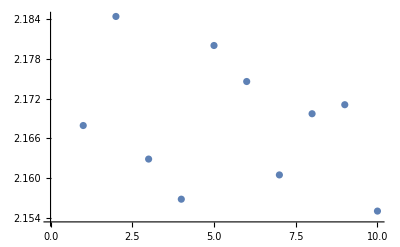

```mathematica
ListPlot[%]
```

```mathematica
ν=df[statdist[1000]]
```

2.18316

★ Test statistic has the form

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))
¬stat \[Distributed] χ^2(ν  ≈ 1.90)
stat\[Distributed] GammaDistribution(α,β)

Distribution of test statistic is chi square — for high lengths of (n ≥ 100) sequences ★ CONSTANT ν ★

```mathematica
mcts
```

{16.5541,24.7637,24.7327,16.5385}

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]-$mcts
```

{13,25,24,19}

Mean counts ratio does not vary with sequence length above a certain length

```mathematica
mcts[n_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],10000]]
```

```mathematica
Table[mcts[n]/n,{n,100,5000,500}]
```

{{0.16553,0.2474,0.24766,0.1661},{0.16612,0.249135,0.24996,0.166392},{0.166419,0.249994,0.249593,0.166629},{0.166518,0.249887,0.249653,0.166768},{0.16661,0.249879,0.24989,0.166915},{0.166819,0.249865,0.249909,0.166517},{0.166449,0.249847,0.249868,0.166547},{0.166895,0.250046,0.250115,0.166822},{0.16656,0.249657,0.250096,0.166809},{0.166622,0.250003,0.24997,0.166721}}

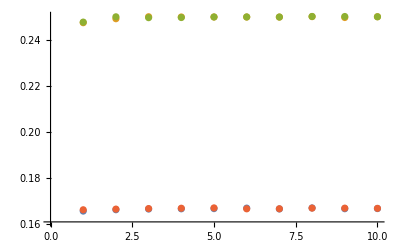

```mathematica
ListPlot[%ᵀ]
```

```mathematica
$mctsrat=mcts[1000]/1000
```

{0.166585,0.249666,0.249679,0.166447}

```mathematica
seqStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)]
```

```mathematica
seqStat/@RandomInteger[{0,1},{10^5,1000}];
```

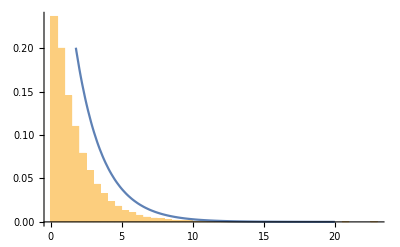

```mathematica
Show[Histogram[%773,Automatic,"Probability",PlotRange->All],Plot[PDF[ChiSquareDistribution[1.9061033494727069],x],{x,0,20}]]
```

```mathematica
FindDistributionParameters[%794,ChiSquareDistribution[n]]
```

{n→1.9061}

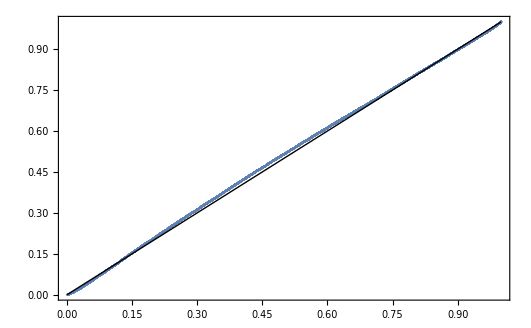

```mathematica
ProbabilityPlot[%794,%812]
```

```mathematica
df[n_]:=degreesOfFreedom/.FindDistributionParameters[seqStat/@RandomInteger[{0,1},{10^5,n}],ChiSquareDistribution[degreesOfFreedom]]
```

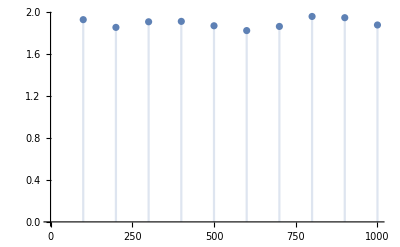

```mathematica
DiscretePlot[df[n],{n,100,1000,100}]
```

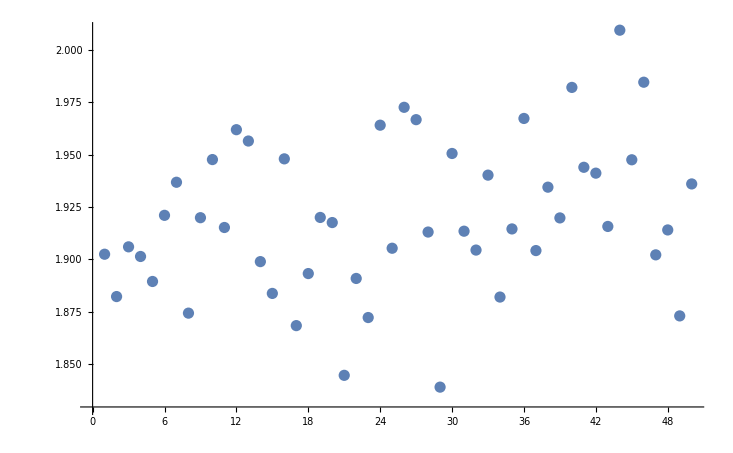

```mathematica
ListPlot[%611]
```

```mathematica
Table[df[n],{n,100,5000,100}];
```

```mathematica
df[1000]
```

1.91098

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Table[1-CDF[ChiSquareDistribution[1.91],seqStat[RandomInteger[{0,1},1000]]],10000];
```

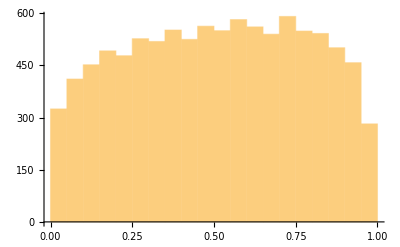

```mathematica
Histogram[%]
```

```mathematica
DistributionFitTest[%750,UniformDistribution[]]
```

0.

Run experiments to show that distribution of stat converges to something else—GammaDistribution?

In paper, note and discuss invariance under list length

```mathematica
FindDistribution[%794,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[1.12244,1.53418]

```mathematica
GammaDistribution
```

```mathematica
Manipulate[Show[Histogram[%794,Automatic,"Probability"],Plot[PDF[%812,x],{x,0,8}]],{ν,0,2}]
```

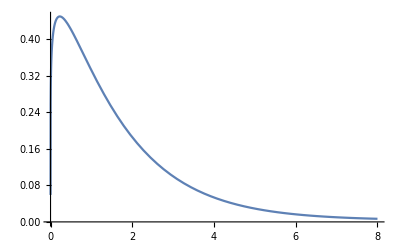

```mathematica
Plot[PDF[%801,x],{x,0,8}]
```

### Procedure & Methods — Outline

Generate a sequence

```mathematica
sequence=RandomInteger[{0,1},100];
sequence//Row
```

1010001010010101011011110011001111011100101110110001100101101011101010011110100011101011001001010010

Format is {{0,0},{0,1},{1,0},{1,1}} for frequency of a sequence.

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{12,30,31,16}

Find a statistic that measures the deviation from expected frequency

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))

Find the mean counts empirically for a given list length n

```mathematica
mcts[n_,samplesize_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],samplesize]]
```

How do these mean counts behave?

```mathematica
Compile[mcts]
```

Compile::argtu: Compile called with 1 argument; 2 or 3 arguments are expected.

Compile[mcts]

```mathematica
ParallelTable[mcts[n,10000]/n,{n,100,1000,100}]
```

{{0.166138,0.247454,0.247369,0.165673},{0.166174,0.248824,0.248729,0.166274},{0.166295,0.248908,0.249039,0.166312},{0.166499,0.249255,0.249211,0.166439},{0.166484,0.249509,0.24975,0.166638},{0.166575,0.249584,0.249569,0.166569},{0.166559,0.249529,0.249706,0.16649},{0.166497,0.249854,0.249716,0.166422},{0.166478,0.249666,0.24974,0.166456},{0.166533,0.249579,0.249745,0.166798}}

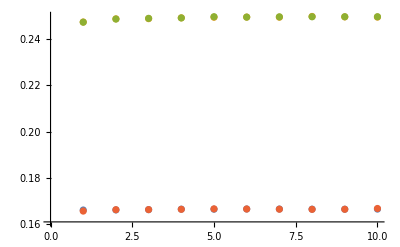

```mathematica
ListPlot[%ᵀ]
```

Ratios between the mean counts and the list length is independent of list length for high (n > 100) list lengths. We can calculate the mean ratios

```mathematica
Compile[{{x,_Real}},mcts[500,x]]
```

CompiledFunction[…]

```mathematica
$mctsrat=Parallelize[(%226[100000])/500]
```

Parallelize::nopar1: (%226[100000])/500 cannot be parallelized; proceeding with sequential evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

{0.166439,0.2495,0.249533,0.166391}

```mathematica
$mctsrat=mcts[500,100000]/500
```

{0.166392,0.249491,0.249536,0.166482}

Generating the statistic is then easy

```mathematica
seqStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)]
```

```mathematica
seqStat[sequence]
```

3.81022

How does this statistic behave?

```mathematica
dist[n_,samplesize_]:=ParallelTable[seqStat[RandomInteger[{0,1},n]],samplesize]
```

```mathematica
distsample500=dist[500,100000];
```

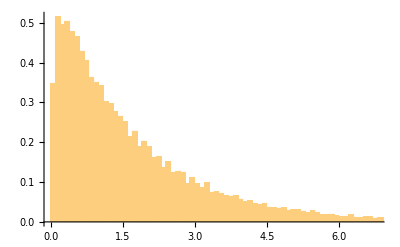

```mathematica
Histogram[distsample500,{.1},"PDF"]
```

This distribution resembles the gamma distribution.

```mathematica
fitdist500=GammaDistribution[α,β]/.FindDistributionParameters[distsample500,GammaDistribution[α,β]]
```

GammaDistribution[1.12973,1.52119]

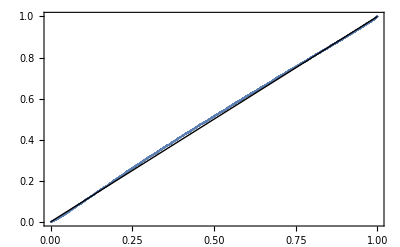

```mathematica
ProbabilityPlot[distsample500,fitdist500]
```

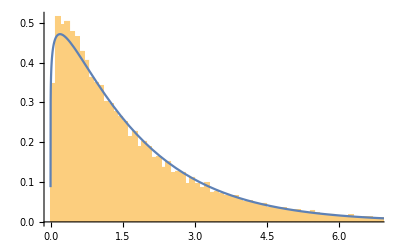

```mathematica
Show[Histogram[distsample500,300,"PDF"],Plot[PDF[fitdist500,x],{x,0,8}]]
```

We can see from the probability plot that this is a very strong fit! We can see that the p-value is low, but not tiny!

```mathematica
DistributionFitTest[distsample500,fitdist500]
```

0.00227318

How do the shape parameters behave with different sequence lengths

```mathematica
αβparams[n_,samplesize_]:=FindDistributionParameters[dist[n,samplesize],GammaDistribution[α,β]]
```

```mathematica
paramvslength=Table[{α,β}/.αβparams[n,10000],{n,100,10000,1000}];
```

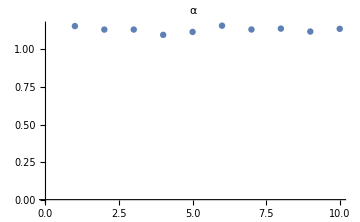
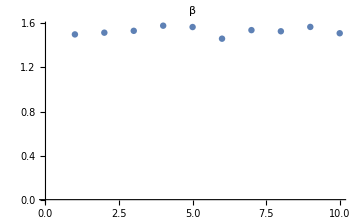

```mathematica
Row@{ListPlot[paramvslengthᵀ⟦1⟧,],ListPlot[paramvslengthᵀ⟦2⟧,]}
```

We can see that the parameters hardly vary and do not vary consistently with list length. We can then find parameters we like.

```mathematica
$params=αβparams[1000,10000]
```

{α→1.12921,β→1.56052}

```mathematica
$fitdist=GammaDistribution[α,β]/.$params
```

GammaDistribution[1.12921,1.56052]

We can now generate p-values

```mathematica
1-CDF[$fitdist,seqStat[sequence]]
```

General::munfl: Exp[-55198.6] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
sequence={1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,1,0,0,1}
```

{1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,1,0,0,1}

```mathematica
1-CDF[$fitdist,seqStat[sequence]]
```

0.261012

```mathematica
1-CDF[$fitdist,seqStat[#]]&/@RandomInteger[{0,1},{100000,100}];
```

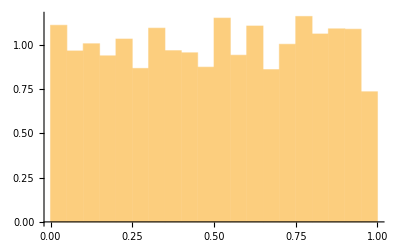

```mathematica
Histogram[%,Automatic,"PDF"]
```

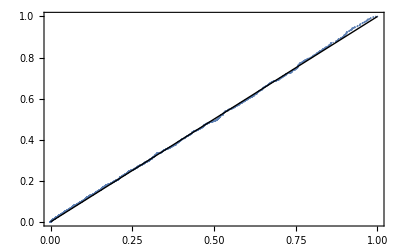

```mathematica
ProbabilityPlot[%977,UniformDistribution[]]
```

We can see that this method is a strong method

```mathematica
1-CDF[$fitdist,seqStat[rule30seq]]
```

0.686934

## ✓ Runs test ★ ★

### Brainstorming 1

How long are runs?

```mathematica
sequence=RandomReal[{0,1},100000];
```

p67

```mathematica
runlengths=Length/@Split[RandomReal[{0,1},10000],#1<#2&];
```

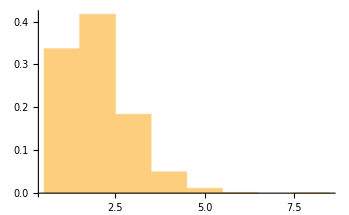

```mathematica
Histogram[%,Automatic,"PDF"]
```

```mathematica
CountsBy[Split[RandomInteger[{0,1},1000]],#⟦1⟧&]
```

<|0→241,1→241|>

```mathematica
runsup[seq_]:=Split[seq,#1<#2&]
```

```mathematica
countRunLength[runsup]
```

<|1→16601,4→2691,2→20833,5→575,3→9118,6→103,7→14,8→3|>

```mathematica
countRunLength[seq_]:=Counts[Length/@Split[seq,#1<#2&]]
```

```mathematica
lengthDist[seq_]:=Length/@runsup[seq]
```

```mathematica
KeyValueMap[#1 #2&,countRunLength[RandomReal[{0,1},1000]]]
```

{384,191,76,306,25,18}

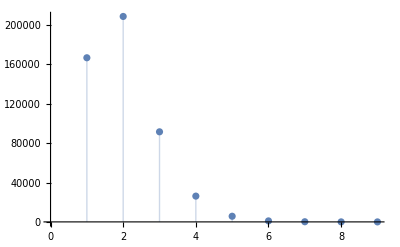

```mathematica
ListPlot[countRunLength[RandomReal[{0,1},1000000]],Filling->Axis]
```

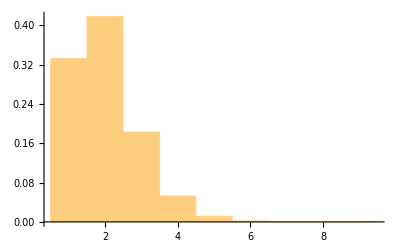

```mathematica
Histogram[lengthDist[RandomReal[{0,1},1000000]],{1},"PDF"]
```

```mathematica
Manipulate[Histogram[lengthDist[Take[sequence,n]],{1},"PDF",PlotRange->{{0,10},{0,1}},PlotLabel->"n = "<>ToString[n]],{n,1,10000,1}]
```

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

```mathematica
runLengthRatios=Counts[lengthDist[RandomReal[{0,1},1000000]]]/1000000.
```

<|2→0.208134,3→0.091811,1→0.166401,4→0.026437,5→0.005795,6→0.000994,7→0.00015,8→0.000019,9→1.×10^-6|>

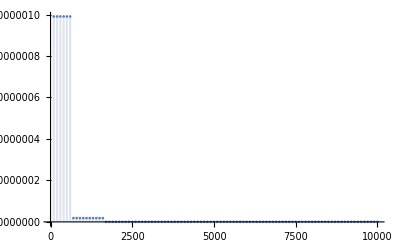

```mathematica
DiscretePlot[Total[Values[KeySort[Append[#1,AssociationThread[Complement[Keys[#1],Keys[#2]]->ConstantArray[0,Length[Complement[Keys[#1],Keys[#2]]]]]]&[runLenthRatios,Counts[lengthDist[Take[#,n]]]/n]-runLenthRatios]]^2],{n,100,10000,100},PlotRange->All]&[RandomReal[{0,1},10000]]
```

Squares difference from 1 million sample distribution length bin counts  vs sample size to constant distribution

```mathematica
$meanRunLengths=Mean[ParallelMap[ N@Mean[Length/@runsup[#]]&,RandomReal[{0,1},{1000,50000}]]]
```

1.9998

```mathematica
meanRunLengthvsSequenceLength=Table[{n, N@Mean[Length/@runsup[RandomReal[{0,1},n]]]},{n,100,10000,500}]
```

{{100,2.04082},{600,1.94805},{1100,1.97842},{1600,2.01005},{2100,1.98675},{2600,2.01238},{3100,1.97452},{3600,2.03275},{4100,2.01672},{4600,2.00786},{5100,2.00236},{5600,1.98371},{6100,2.02658},{6600,1.97723},{7100,2.01361},{7600,1.99737},{8100,1.99507},{8600,1.99629},{9100,1.99868},{9600,2.01174}}

```mathematica
runLengthDistvsSequenceLength=Table[{n, N@Identity[Length/@runsup[RandomReal[{0,1},n]]]},{n,100,10000,500}]
```

{{100,{1.,1.,3.,1.,2.,3.,2.,1.,4.,2.,3.,3.,1.,2.,3.,2.,2.,3.,1.,1.,1.,3.,3.,1.,2.,2.,1.,1.,3.,2.,3.,3.,3.,1.,2.,1.,2.,1.,2.,3.,3.,3.,4.,1.,2.,1.,1.,3.,1.}},18,{9600,{2.,2.,2.,1.,2.,1.,1.,4750,2.,3.,2.,2.,2.,1.,1.}}}
 |  |  |  |

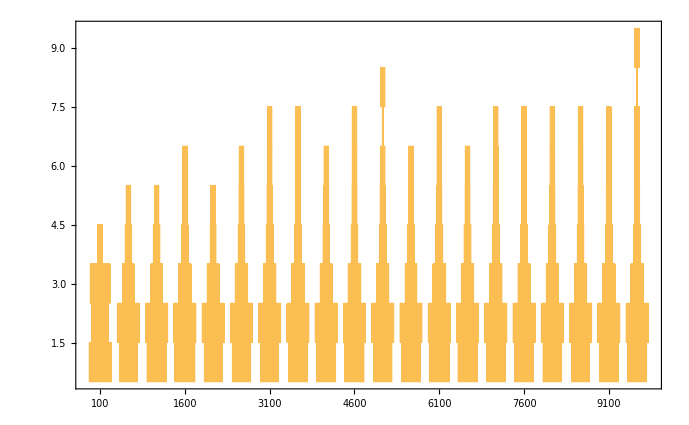

```mathematica
DistributionChart[runLengthDistvsSequenceLengthᵀ⟦2⟧,ChartElementFunction->"HistogramDensity",ChartLabels->runLengthDistvsSequenceLengthᵀ⟦1⟧,PlotRange->{0,All}]
```

Figure above: Runs up lengths vs. sequence length

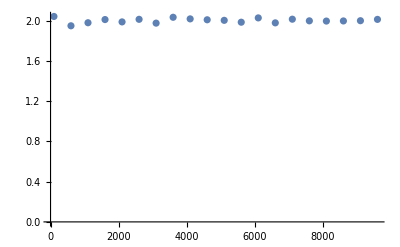

```mathematica
ListPlot[meanRunLengthvsSequenceLength,PlotRange->{0,All}]
```

Figure above: Runs up mean lengths do not vary with sample size

```mathematica
LinearModelFit[meanRunLengthvsSequenceLength,x,x]["RSquared"]
```

0.0644988

```mathematica
$meanRunLengths=N@Mean[Table[Mean[Length/@runsup[RandomReal[{0,1},5000]]],1000]]
```

1.99997

```mathematica
stat[seq_]:=Total[(seq-$meanRunLengths)^2/($meanRunLengths)]
```

```mathematica
stat[seq_]:=Total[(Length/@runsup[seq]-$meanRunLengths)^2/($meanRunLengths)]
```

```mathematica
statdist[sequenceLength_,n_]:=stat[#]&/@RandomReal[{0,1},{n,sequenceLength}]
```

```mathematica
Manipulate[ProbabilityPlot[statdist[seqleng,1000]],{seqleng,10000}]
```

```mathematica
DistributionFitTest[statdist[600,1000],NormalDistribution[statdistμ[600],statdistσ[600]]]
```

0.0970035

Figure above: The statistic strongly follows a normal distribution

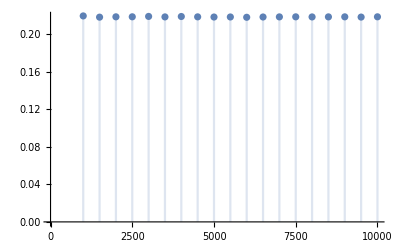

```mathematica
DiscretePlot[μ/seqleng/.FindDistributionParameters[statdist[seqleng,1000],NormalDistribution[μ,σ]],{seqleng,1000,10000,500}]
```

The mean of the distribution varies linearly with the sequence length.

```mathematica
statdistμ[seqleng_]=seqleng μ/10000/.FindDistributionParameters[statdist[10000,10000],NormalDistribution[μ,σ]]
```

0.218195 seqleng

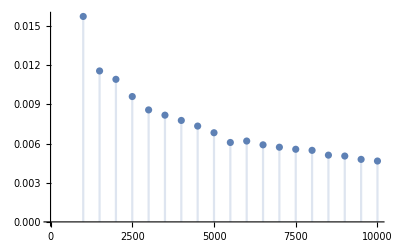

```mathematica
DiscretePlot[σ/seqleng/.FindDistributionParameters[statdist[seqleng,1000],NormalDistribution[μ,σ]],{seqleng,1000,10000,500}]
```

```mathematica
standarddevratvsseqleng=ParallelTable[{seqleng,σ/seqleng}/.FindDistributionParameters[statdist[seqleng,1000],NormalDistribution[μ,σ]],{seqleng,1000,10000,500}];
```

```mathematica
nlm=NonlinearModelFit[standarddevratvsseqleng,a x^b,{a,b},x]
```

FittedModel[0.549569/x^0.518374]

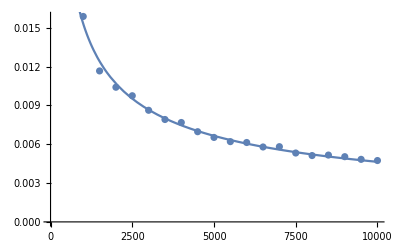

```mathematica
Show[ListPlot[standarddevratvsseqleng],Plot[nlm[seqleng],{seqleng,0,10000}]]
```

σ/seqleng≈nlm[seqleng]
σ≈sqeleng nlm[seqleng]

```mathematica
seqleng nlm[seqleng]
```

0.549569 seqleng^0.481626

```mathematica
statdistσ[seqleng_]=0.4208000593890539 seqleng^0.503677726169205
```

0.4208 seqleng^0.503678

stat \[Distributed] NormalDistribution[statdistμ[seqleng],statdistσ[seqleng]]

```mathematica
stdev[100000]
```

138.824

```mathematica
stat[sequence]
```

116215.

```mathematica
CDF[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[sequence]]
```

0.

```mathematica
Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[RandomReal[{0,1},2000]]]
```

0.248275

Test the rate of type 1 error — success!

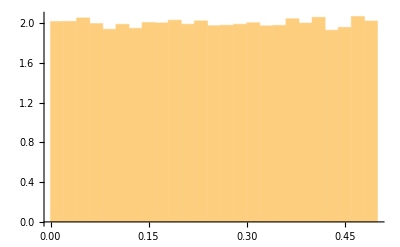

```mathematica
Histogram[Table[Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[RandomReal[{0,1},2000]]],100000],Automatic,"PDF"]
```

```mathematica
Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[RandomReal[{0,1},2000]]]
```

0.244446

### Implementing

```mathematica
Table[ResourceFunction[LocalObject["file:///Users/noahb32/Library/Wolfram/Objects/DeployedResources/Function/RunLengthRandomnessTest"]][RandomReal[{0,1},10000]],1000];
```

### Brainstorming 2

How many runs do we expect a sequence to have?

```mathematica
binomialFit[samp_]:=FindDistributionParameters[samp,BinomialDistribution[n,p]]
```

```mathematica
binommodelvar1 =Table[binomialFit[Length[Split[#,(#1<#2&)]]&/@RandomReal[{0,1},{1000,nn}]],{nn,1000,10000,1000}]
```

{{n→597,p→0.838211},{n→1208,p→0.828469},{n→1815,p→0.826514},{n→2404,p→0.832156},{n→3010,p→0.830896},{n→3591,p→0.835859},{n→4198,p→0.833928},{n→4793,p→0.834603},{n→5410,p→0.832169},{n→6001,p→0.833213}}

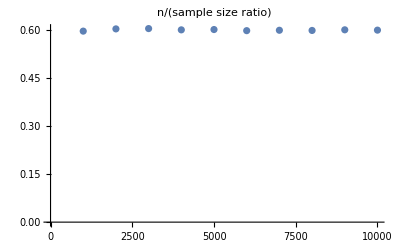

```mathematica
ListPlot[{Table[nn,{nn,1000,10000,1000}],(n/.#&/@binommodelvar1)/Table[nn,{nn,1000,10000,1000}]}ᵀ,]
```

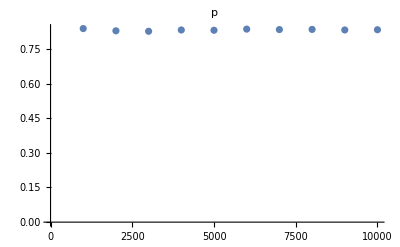

```mathematica
ListPlot[{Table[nn,{nn,1000,10000,1000}],p/.#&/@binommodelvar1}ᵀ,]
```

```mathematica
Mean[N@p/.#&/@binommodelvar1]
```

0.832602

```mathematica
Mean[N@n/.#&/@binommodelvar1]
```

0.832602

```mathematica
BinomialDistribution[0.6007550396825396 n,0.8326016102887464]
```

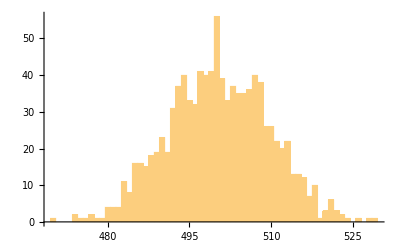

```mathematica
Histogram[%758,100]
```

```mathematica
Length[%758]
```

1000

```mathematica
FindDistributionParameters[%758,BinomialDistribution[n,p]]
```

{n→603,p→0.829773}

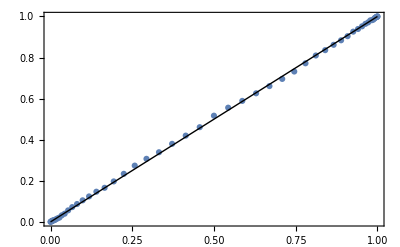

```mathematica
ProbabilityPlot[%758,BinomialDistribution[Round@(0.6007550396825396 1000),0.8326016102887464]]
```

```mathematica
numberOfRunsStat=Length@Split[#,(#1<#2&)]&
```

Length[Split[#1,#1<#2&]]&

```mathematica
numberOfRunsDistribution[seqleng_]:=BinomialDistribution[Round@(0.6007550396825396  seqleng),0.8326016102887464]
```

```mathematica
RandomReal[{0,1},{1000,1000}]
```

$Aborted[]

```mathematica
numberOfRunsStat/@RandomReal[{0,1},{1000,100}];
```

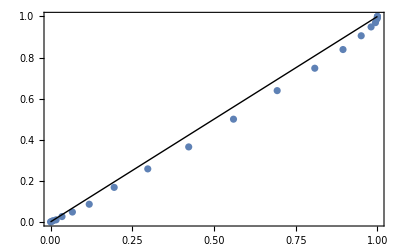

```mathematica
ProbabilityPlot[%,numberOfRunsDistribution[100]]
```

```mathematica
DistributionFitTest[numberOfRunsStat/@RandomReal[{0,1},{1000,500}],numberOfRunsDistribution[500]]
```

0.0717908

### Implementing 2

```mathematica
Table[{{"[◼]", "RunCountRandomnessTest"}}[RandomReal[{0,1},1000]],10000];
```

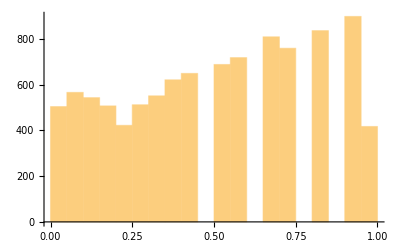

```mathematica
Histogram[%]
```

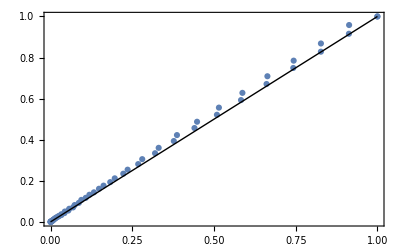

```mathematica
ProbabilityPlot[%%,UniformDistribution[{0,1}]]
```

## ✓ Differences tests

### Brainstorming — First Order

#### Random Reals

```mathematica
sequence=RandomReal[{0,1},100000];
```

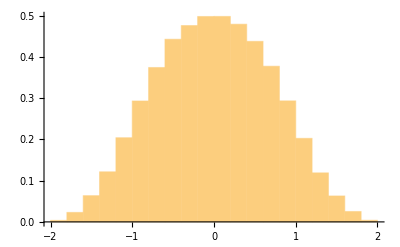

```mathematica
Histogram[Differences[sequence,2],Automatic,"PDF"]
```

```mathematica
TransformedDistribution[X-n,X\[Distributed]UniformSumDistribution[n]]
```

UniformSumDistribution[n,{-1,0}]

```mathematica
TransformedDistribution[X-3,X\[Distributed]UniformSumDistribution[3]]
```

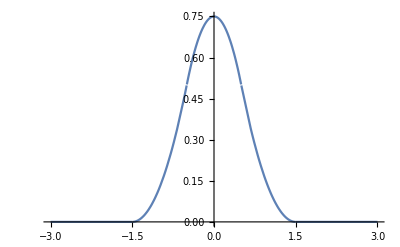

```mathematica
Plot[PDF[TransformedDistribution[X-3/2,X\[Distributed]UniformSumDistribution[3]],x],{x,-3,3}]
```

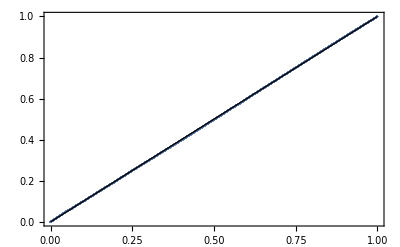

```mathematica
ProbabilityPlot[Differences[sequence,1],TransformedDistribution[X-2/2,X\[Distributed]UniformSumDistribution[2]]]
```

```mathematica
sequence=RandomReal[{0,1},1000];
```

```mathematica
KolmogorovSmirnovTest[Differences[sequence,1],TransformedDistribution[X-1,X\[Distributed]UniformSumDistribution[2]]]
```

0.606071

#### Random 0s and 1s

```mathematica
sequence=RandomInteger[{0,1},1000];
```

```mathematica
ArrayPlot[{sequence},ImageSize->Full]
```

-Graphics-

```mathematica
Histogram[Differences[sequence],Automatic,"PDF"]
```

### Brainstorming — nth Order

Consider a random sequence

{x_1,x_2,x_3,x_4,x_5,⋯,x_(n-2),x_(n-1),x_n}

## ✓ Overlapping permutations (OPERM5)

### Brainstorm

```mathematica
sequence=RandomInteger[{0,1},100];
```

```mathematica
Tuples[{0,1},5]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

```mathematica
$cts=Values@KeySort@(CountsBy[Tuples[{0,1},5],Total]/(N@Length[Tuples[{0,1},5]]))
```

{0.03125,0.15625,0.3125,0.3125,0.15625,0.03125}

```mathematica
N@PadRight[Values@KeySort@(Counts[Total/@Subsequences[RandomInteger[{0,1},500],{5}]]/Length[Subsequences[RandomInteger[{0,1},500],{5}]]),6]
```

{0.00604839,0.163306,0.318548,0.284274,0.183468,0.0443548}

```mathematica
Length[Subsequences[RandomInteger[{0,1},1000],{5}]]
```

996

```mathematica
OPERM5stat=Total[(PadRight[Values@KeySort@(Counts[Total/@Subsequences[#,{5}]]/(Length[#]-4)),6]-$cts)^2/$cts]&;
```

```mathematica
FindDistributionParameters[Table[stat[RandomInteger[{0,1},100]]]
```

0.919444

```mathematica
stat/@RandomInteger[{0,1},{10^4,100}];
```

```mathematica
Parallelize@Table[{n,β}/.FindDistributionParameters[stat/@RandomInteger[{0,1},{10^4,n}],GammaDistribution[α,β]],{n,1000,5000,500}]
```

{{1000,0.00590491},{1500,0.00399195},{2000,0.00304273},{2500,0.00240713},{3000,0.00200832},{3500,0.00173703},{4000,0.00153407},{4500,0.0013323},{5000,0.00119603}}

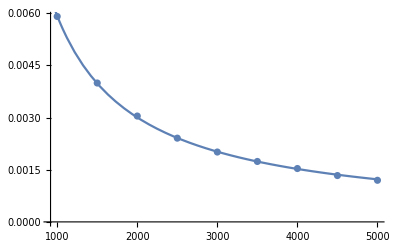

```mathematica
Show[ListPlot[%499],Plot[%509[x],{x,0,5000}]]
```

```mathematica
OPERM5αvsn=Table[{n,α}/.FindDistributionParameters[OPERM5stat/@RandomInteger[{0,1},{10^4,n}],GammaDistribution[α,β]],{n,1000,5000,500}]
```

$Aborted

```mathematica
αOPERM5=Mean[OPERM5αvsnᵀ⟦2⟧]
```

```mathematica
αOPERM5=2.0568433064986755
```

2.05684

```mathematica
βOPERM5[seqleng_]=%509[seqleng]
```

%509[seqleng]

```mathematica
βOPERM5[seqleng_]:=5.154091641671948/seqleng^0.9799168145415045
```

```mathematica
NonlinearModelFit[%499,a x^b,{a,b},x]
```

FittedModel[5.15409/x^0.979917]

```mathematica
Table[OPERM5stat[RandomInteger[{0,1},240]],1000];
```

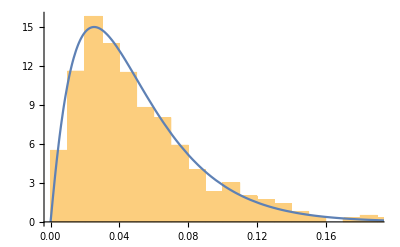

```mathematica
Show[Histogram[%,Automatic,"PDF"],Plot[PDF[OPERM5dist[240],x],{x,0,1},PlotRange->All]]
```

```mathematica
DistributionFitTest[%69,OPERM5dist[240]]
```

0.0497884

```mathematica
FindDistribution[%430,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[2.03343,0.0120271]

```mathematica
OPERM5dist[seqleng_]:=GammaDistribution[αOPERM5,βOPERM5[seqleng]]
```

```mathematica
OPERM5stat[RandomInteger[{0,1},100000]]
```

0.0000430466

The test displays expected type I error!

```mathematica
Table[1-CDF[OPERM5dist[1000],OPERM5stat[RandomInteger[{0,1},1000]]],10000];
```

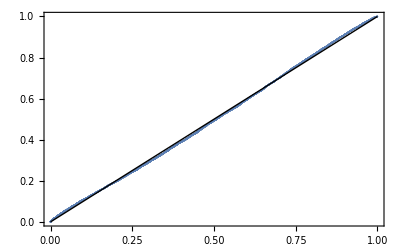

```mathematica
ProbabilityPlot[%,UniformDistribution[]]
```

```mathematica
1-CDF[OPERM5dist[Length[rule30seq]],OPERM5stat[rule30seq]]
```

0.764675

Rule 30 seems to be random!

## ✓ Autocorrelation (already implemented)

```mathematica
AutocorrelationTest[Take[N@rule30seq,1000],Automatic,{"TestDataTable",All}]
```

| Statistic | P-Value
Box-Pierce | 11.6261 | 0.113546
Ljung-Box | 11.6915 | 0.11117

## Gap tests

Only on random reals
Page 62 ★

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},1000];
```

## Spectral Tests

## Overlapping sums (OSUMn)

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},100000];
```

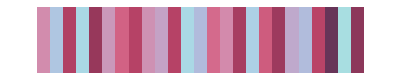

```mathematica
ArrayPlot[{RandomSample[sequence,25]},ColorFunction->"CandyColors",AspectRatio->Automatic,ImageSize->Full]
```

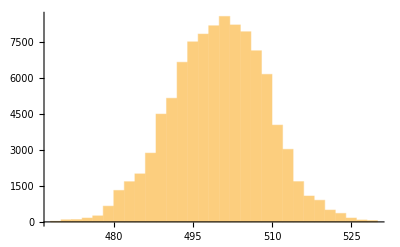

```mathematica
Histogram[Total/@Subsequences[sequence,{1000}]]
```

```mathematica
UniformSumDistribution[100]
```

UniformSumDistribution[100,{0,1}]

```mathematica
FindDistributionParameters[Total/@Subsequences[sequence,{1000}],NormalDistribution[μ,σ]]
```

{μ→499.736,σ→8.63983}

```mathematica
GammaDistribution[α,β]/.FindDistributionParameters[Total/@Subsequences[RandomReal[{0,1},100000],{1000}],GammaDistribution[α,β]]
```

GammaDistribution[3225.7,0.154501]

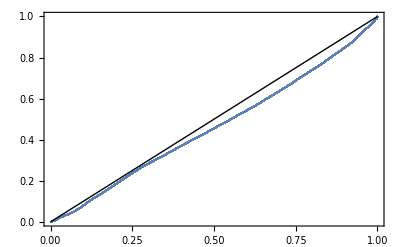

```mathematica
ProbabilityPlot[Total/@Subsequences[RandomReal[{0,1},100000],{1000}],GammaDistribution[3225.6994588174252,0.1545010290874235]]
```

```mathematica
LocationTest[Total/@Subsequences[sequence,{100}],50]
```

0.260026

```mathematica
Total/@Subsequences[sequence,{100}]
```

{45.2962,45.5133,45.5919,45.1799,44.6169,44.5231,99889,51.2486,51.3479,52.2374,52.1626,51.9738,52.9498}
 |  |  |  |

```mathematica
DistributionFitTest[Total/@Subsequences[RandomReal[{0,1},10000],{5}]]
```

0.00606352

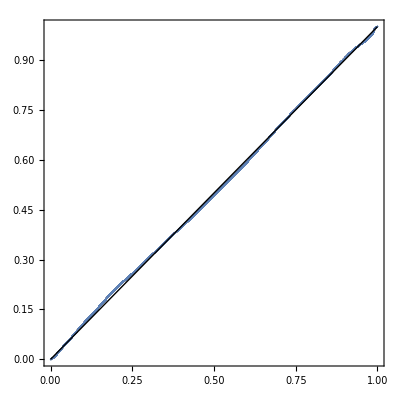

```mathematica
ProbabilityPlot[Total/@Subsequences[RandomReal[{0,1},100000],{1000}],AspectRatio->1]
```

```mathematica
OSUMnstatχ[seq_,n_]:=Total[(Mean/@Subsequences[seq,{n}]-1/2)^2/(1/2)]
```

```mathematica
Total/@Subsequences[sequence,{1000}]
```

{508.647,508.662,508.429,509.252,509.795,510.408,510.823,510.645,511.177,511.124,511.2,510.883,511.113,98975,502.805,503.203,502.821,503.207,502.791,501.948,501.953,502.789,503.213,503.146,502.98,503.252,503.062}
 |  |  |  |

```mathematica
OSUMnstatχ[Random,10]
```

1653.49

```mathematica
OSUMnstatmean[seq_,n_]:=Mean[Mean/@Subsequences[seq,{n}]]
```

```mathematica
sequence
```

```mathematica
Total[(Total/@Subsequences[sequence,{100}]-.5 100)^2/(.5  100)]
```

17536.7

```mathematica
Table[Total[(Mean/@Subsequences[RandomReal[{0,1},1000],{100}]-.5)^2/(.5)],1000]
```

```mathematica
GammaDistribution[α,β]/.FindDistributionParameters[%609,GammaDistribution[α,β]]
```

GammaDistribution[7.62933,0.194779]

```mathematica
DistributionFitTest[%609,GammaDistribution[7.629327599137594,0.19477924125305393]]
```

0.551077

```mathematica
Length[Total/@Subsequences[sequence,{100}]]
```

99901

```mathematica
DiscretePlot[OSUMnstatmean[sequence,n],{n,5,50000,10000}]
```

$Aborted[]

```mathematica
OSUMnstatmean[sequence,1000]/1000
```

0.49987

```mathematica
1/2 n
```

```mathematica
OSUMnstatmean[#,10]&/@RandomReal[{0,1},{10000,1000}];
```

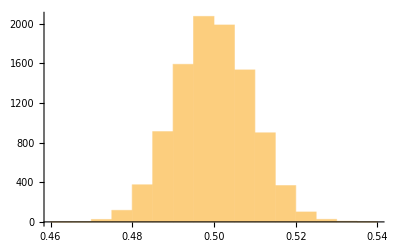

```mathematica
Histogram[%161]
```

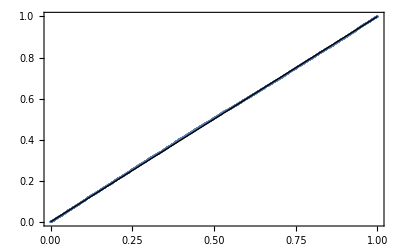

```mathematica
ProbabilityPlot[%161]
```

```mathematica
KolmogorovSmirnovTest[%31]
```

0.844567

```mathematica
Table[{seqleng,StandardDeviation[OSUMnstatmean[#,100]&/@RandomReal[{0,1},{1000,seqleng}]]},{seqleng,1000,10000,1000}]
```

{{1000,0.00926192},{2000,0.00660548},{3000,0.00523465},{4000,0.00448585},{5000,0.00406819},{6000,0.00379244},{7000,0.00345482},{8000,0.0032889},{9000,0.00307945},{10000,0.00287389}}

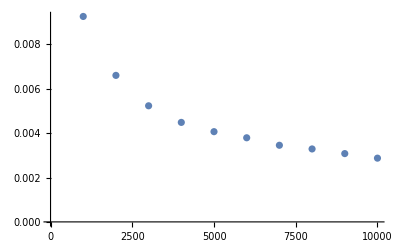

```mathematica
ListPlot[%37]
```

```mathematica
NonlinearModelFit[%37,a x^b,{a,b},x]
```

FittedModel[0.306693/x^0.506635]

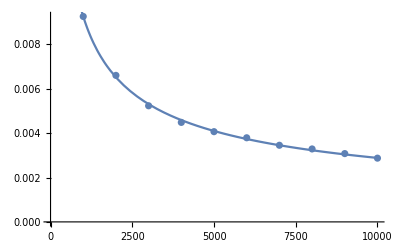

```mathematica
Show[ListPlot[%37],Plot[%41[x],{x,0,10000}]]
```

```mathematica
NormalDistribution[.5,%41[10000]]
```

```mathematica
OSUMnstatmean[#,100]&/@RandomReal[{0,1},{10000,10000}];
```

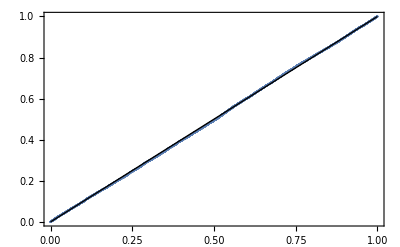

```mathematica
ProbabilityPlot[%48,NormalDistribution[.5,%41[10000]]]
```

## Maximum test

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},1000];
```

```mathematica
Mean@TakeLargest[sequence,50]
```

0.979701

```mathematica
Table[Times[##/.List->Sequence]&@TakeLargest[RandomReal[{0,1},1000],50],10000];
```

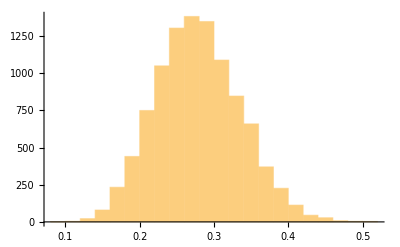

```mathematica
Histogram[%]
```

```mathematica
CDF[BetaDistribution[1000,1],Max[sequence]]
```

0.862772

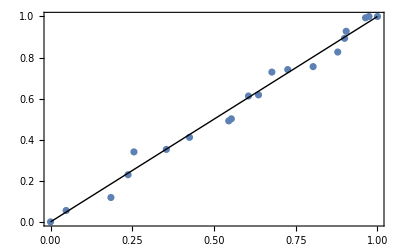

```mathematica
ProbabilityPlot[%90,BetaDistribution[1,100]]
```

```mathematica
DistributionFitTest[%90,BetaDistribution[1,1000]]
```

2.33846×10^-8

```mathematica
N@StandardDeviation[TransformedDistribution[X+ Y+Z,{X\[Distributed]BetaDistribution[1,1000],Y\[Distributed]BetaDistribution[999,2],Z\[Distributed]BetaDistribution[998,3]}]]
```

0.00244297

```mathematica
OrderDistribution[{UniformDistribution[],1000},{1000,999}]
```

OrderDistribution[{UniformDistribution[{0,1}],1000},{1000,999}]

```mathematica
PDF[BetaDistribution[100,1],x]
```

Piecewise[{{100 x^99, 0<x<1}, {0, True}}]

```mathematica
`
```